### Start choosing the example:

```mathematica
t=2;
beta=0;
A=0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{2,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.006962,Null}

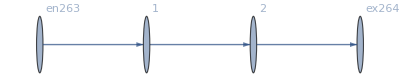

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j265→80.,j266→80.,j267→80.,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80.,jt273→80.,jt274→0.,u275→95.,u276→15.,u277→95.,u278→15.,u279→15.,u280→95.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→17.582}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

EEX: newrules when Head is Equal: {{u275→17.582}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→17.582,u276→15.,u277→17.582,u278→15.,u279→15.,u280→17.582|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→18.1613}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

EEX: newrules when Head is Equal: {{u275→18.1613}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→18.1613,u276→15.,u277→18.1613,u278→15.,u279→15.,u280→18.1613|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→20.0239}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

EEX: newrules when Head is Equal: {{u275→20.0239}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→20.0239,u276→15.,u277→20.0239,u278→15.,u279→15.,u280→20.0239|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: newrules when Head is Equal: {{u275→95.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.52651×10^-14,ComplexInfinity]

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→95.,u276→15.,u277→95.,u278→15.,u279→15.,u280→95.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→378.906}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u275→378.906}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→378.906,u276→15.,u277→378.906,u278→15.,u279→15.,u280→378.906|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→290058.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u275→290058.}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→290058.,u276→15.,u277→290058.,u278→15.,u279→15.,u280→290058.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→1.5595×10^7}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u275→1.5595×10^7}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→1.5595×10^7,u276→15.,u277→1.5595×10^7,u278→15.,u279→15.,u280→1.5595×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→2.40526×10^10}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u275→2.40526×10^10}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→2.40526×10^10,u276→15.,u277→2.40526×10^10,u278→15.,u279→15.,u280→2.40526×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→5.6037×10^18}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u275→5.6037×10^18}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→5.6037×10^18,u276→15.,u277→5.6037×10^18,u278→15.,u279→15.,u280→5.6037×10^18|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

EEX: newrules when Head is Equal: {{u275→2.2049×10^106}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

EEX: newrules when Head is Equal: {{u275→2.2049×10^106}}

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→0.,j269→0.,j270→0.,jt271→0.,jt272→80,jt273→80,jt274→0.,u275→2.2049×10^106,u276→15.,u277→2.2049×10^106,u278→15.,u279→15.,u280→2.2049×10^106|>